```mathematica
TransformedDistribution[x+y,{x\[Distributed]BinomialDistribution[Subscript[n, 1],p],y\[Distributed]BinomialDistribution[Subscript[n, 2],p] }]
```

BinomialDistribution[n_1+n_2,1/6]

```mathematica
{μ,σ}={Mean[BinomialDistribution[n,p]],StandardDeviation[BinomialDistribution[n,p]]}
```

{n/6,(√5 √n)/6}

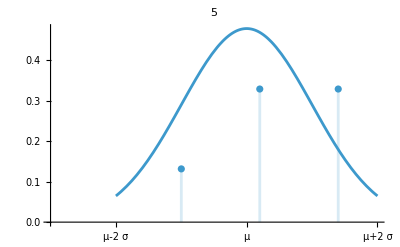
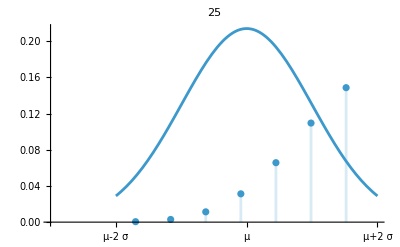
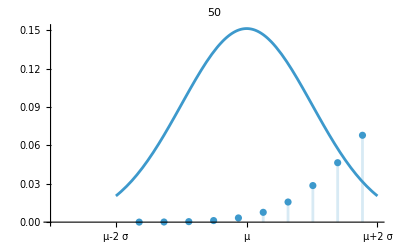
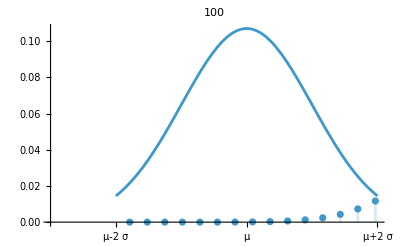

```mathematica
Block[{p=1/3},
Table[Show[DiscretePlot[PDF[BinomialDistribution[n,p],k],{k,Ceiling[μ-2σ],Floor[μ+2σ]},PlotRange->{{μ-3σ,μ+2σ},All},AxesOrigin->{μ-3σ,0}],Plot[PDF[NormalDistribution[μ,σ],x],{x,μ-2σ,μ+2σ}],Ticks->{{{μ-2σ,HoldForm[μ-2σ]},{μ,HoldForm[μ]},{μ+2σ,HoldForm[μ+2σ]}},Automatic},PlotRange->{{μ-3σ,μ+2σ},All},PlotLabel->n],{n,{5,25,50,100}}]]
```

```mathematica
Table[PDF[BinomialDistribution[1,p],k],{k,0,1}]
```

{5/6,1/6}

```mathematica
Table[PDF[BernoulliDistribution[p],k],{k,0,1}]
```

{5/6,1/6}